Sin[n π]/(n π)

(1-Cos[n π])/(n π)

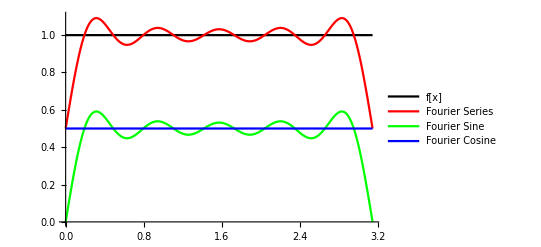

```mathematica
(*Problem #8 part a*)
Clear[a,b,M,x,n,L,f]
a[n_]:=Integrate[f[x]*Cos[(n*Pi/L)*x],{x,0,L}]*(1/(L))
b[n_]:=Integrate[f[x]*Sin[(n*Pi/L)*x],{x,0,L}]*(1/(L))
f[x_]:=1
L:=Pi
a[n]
b[n]

myFCos[x_,M_]:=Sum[a[n]*Cos[(n*Pi/L)*x],{n,1,M}]+a[0]/2
myFSin[x_,M_]:=Sum[b[n]*Sin[(n*Pi/L)*x],{n,0,M}]

Plot[{f[x],Evaluate[myFCos[x,10]+myFSin[x,10]],Evaluate[myFSin[x,10]],Evaluate[myFCos[x,10]]},{x,0,L},PlotRange->{0,f[L]+0.1},PlotStyle->{Black,Red,Green,Blue},PlotLegends->{"f[x]","Fourier Series","Fourier Sine","Fourier Cosine"}]
(*Graph of part a f(x) = 1*)
```

(2 Sin[n π])/(n π)

(-2 n π Cos[n π]+2 Sin[n π])/(n^2 π)

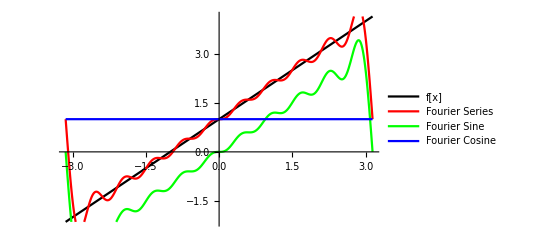

```mathematica
(*Problem #8 part b f(x) = 1+x*)
Clear[a,b,M,x,n,L,f]
a[n_]:=Integrate[f[x]*Cos[(n*Pi/L)*x],{x,-L,L}]*(1/(L))
b[n_]:=Integrate[f[x]*Sin[(n*Pi/L)*x],{x,-L,L}]*(1/(L))
f[x_]:=1+x
L:=Pi
a[n]
b[n]

(*Here is where i form sine and cosing series expansion*)
myFCos[x_,M_]:=Sum[a[n]*Cos[(n*Pi/L)*x],{n,1,M}]+a[0]/2
myFSin[x_,M_]:=Sum[b[n]*Sin[(n*Pi/L)*x],{n,0,M}]

(*Here is where i form the plot*)
Plot[{f[x],Evaluate[myFCos[x,10]+myFSin[x,10]],Evaluate[myFSin[x,10]],Evaluate[myFCos[x,10]]},{x,-L,L},PlotRange->{f[-L],f[L]},PlotStyle->{Black,Red,Green,Blue},PlotLegends->{"f[x]","Fourier Series","Fourier Sine","Fourier Cosine"}]
(*Graph of part b f(x) = 1+x*)
```

Sin[n π]/(n π)

(n π-3 n π Cos[n π]+2 Sin[n π])/(n^2 π^2)

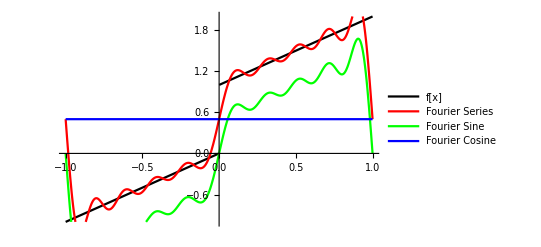

```mathematica
(*Problem #8 part c f(x) is a piecewise defined function*)
f[x_]:=Piecewise[{{x,x>=-L&&x<0},{1+x,x>0&&x<=L}}]
L:=1
a[n]
b[n]

(*Here is where i form sine and cosing series expansion*)
myFCos[x_,M_]:=Sum[a[n]*Cos[(n*Pi/L)*x],{n,1,M}]+a[0]/2
myFSin[x_,M_]:=Sum[b[n]*Sin[(n*Pi/L)*x],{n,0,M}]

(*Here is where i form the plot*)
Plot[{f[x],Evaluate[myFCos[x,10]+myFSin[x,10]],Evaluate[myFSin[x,10]],Evaluate[myFCos[x,10]]},{x,-L,L},PlotRange->{f[-L],f[L]},PlotStyle->{Black,Red,Green,Blue},PlotLegends->{"f[x]","Fourier Series","Fourier Sine","Fourier Cosine"}]
(*Graph of part c f(x) piecewise*)
(*Notice that the jump of the 'x' part and '1+x'*)
```

Sin[n π]/(n π)

(1-Cos[n π])/(n π)

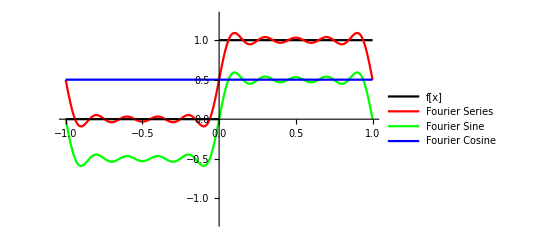

```mathematica
(*Problem #7 part d f(x) is a piecewise defined function*)
f[x_]:=Piecewise[{{0,x>=-L&&x<0},{1,x>0&&x<=L}}]
L:=1
a[n]
b[n]

(*Here is where i form sine and cosing series expansion*)
myFCos[x_,M_]:=Sum[a[n]*Cos[(n*Pi/L)*x],{n,1,M}]+a[0]/2
myFSin[x_,M_]:=Sum[b[n]*Sin[(n*Pi/L)*x],{n,0,M}]

(*Here is where i form the plot*)
Plot[{f[x],Evaluate[myFCos[x,10]+myFSin[x,10]],Evaluate[myFSin[x,10]],Evaluate[myFCos[x,10]]},{x,-L,L},PlotRange->{-1.3,1.3},PlotStyle->{Black,Red,Green,Blue},PlotLegends->{"f[x]","Fourier Series","Fourier Sine","Fourier Cosine"}]
(*Graph of part d piecewise*)
(*Notice that the graph switches form 0 and 1 at the origin*)
```